```mathematica
alphaAbove=2.575199391296956;
Ebreak=1.3491856809517384;
alphaBelow=1.1107351768821663;
ErgsPerGeV=0.00160218;
(*2 kpc cut:*)
alphaAbove = 2.6067763644623803;
alphaBelow = 1.2520410418085917;
Ebreak = 1.6363907062946;bpl[energy_]:=Piecewise[{{(energy/Ebreak)^-alphaAbove, energy > Ebreak}, {(energy/Ebreak)^-alphaBelow, energy <= Ebreak}}]
```

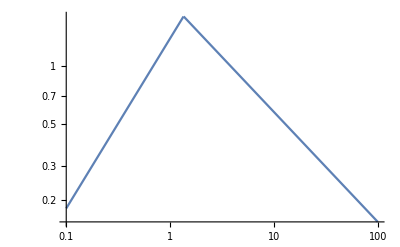

```mathematica
LogLogPlot[energy^2 bpl[energy], {energy, 0.1, 100}]
```

```mathematica
Elow=0.1;
Ehigh=100;
Elow=1.893;
Ehigh=11.943;
Integrate[energy bpl[energy], {energy, Elow, Ehigh}]/Integrate[bpl[energy], {energy, Elow, Ehigh}]
Integrate[energy bpl[energy], {energy, Elow, Ehigh}]/Integrate[bpl[energy], {energy, Elow, Ehigh}]*ErgsPerGeV
```

3.55781

0.00570026